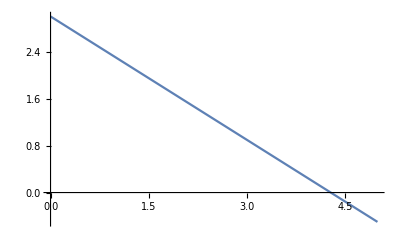

```mathematica
r[θ_]:=rmax-s θ;
s=0.7;
rmax=3;
Plot[r[θ],{θ,0,5}]
```

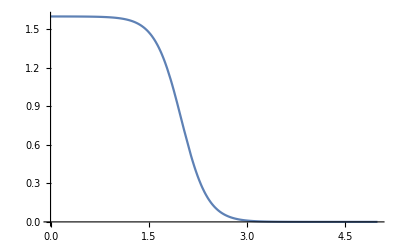

```mathematica
g[x_,θ_]:=r[θ]/(1+Exp[a(x-θ)]);
a=5;
p1=Plot[g[x,2],{x,0,5},PlotRange->Full]
```

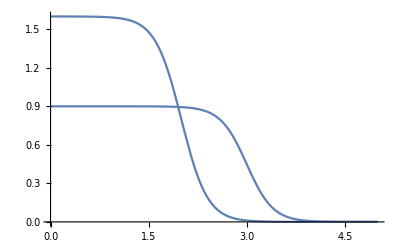

```mathematica
p2=Plot[g[x,3],{x,0,5},PlotRange->Full];
Show[{p1,p2}]
```

```mathematica
g[1.0,2.0]
```

1.58929

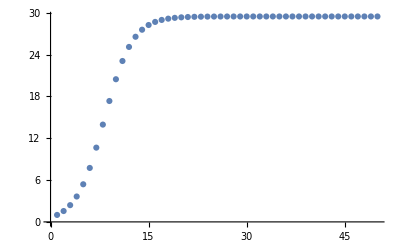

```mathematica
w[n_,x_,θ_]:=g[x,θ]-n/k;
k=50;
p1=ListPlot[RecurrenceTable[
{n[t]==w[n[t],1.0,2.0] n[t-1],n[1]==1},n,{t,1,50}],PlotRange->Full]
```

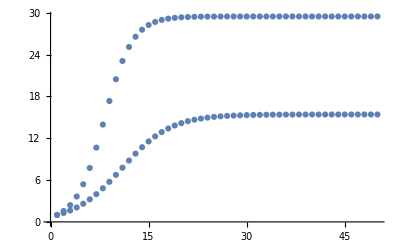

```mathematica
p2=ListPlot[RecurrenceTable[
{n[t]==w[n[t],1.7,2.0] n[t-1],n[1]==1},n,{t,1,50}],PlotRange->Full];
Show[{p1,p2}]
```

```mathematica
(* Transition matrix *)
Λ=({{1-m, m}, {m, 1-m}})({{w1, 0}, {0, w2}})
```